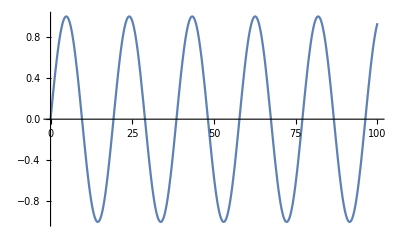

```mathematica
SetDirectory[NotebookDirectory[]];
n=0;
SeedRandom[0];
fn=Total@Table[Sin[ RandomReal[]/2 x],{i,0,n}];
Plot[fn,{x,0,100}]
```

```mathematica
fn
```

Sin[0.326234 x]

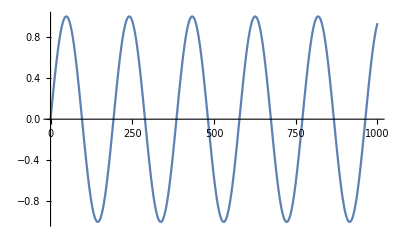

```mathematica
dx=.1;
dat=Table[{x/dx,fn},{x,0,100,dx}];
Export["data.dat",dat[[All,2]],"Table"];
ListPlot[dat,Joined->True]
```

```mathematica
pars={.326234};
fn2=Total@Table[Sin[pars[[i]]*c*dx],{i,1,Length[pars]}]
```

Sin[0.0326234 c]

```mathematica
Sin[0.102706 c]/.c->1
```

0.102526

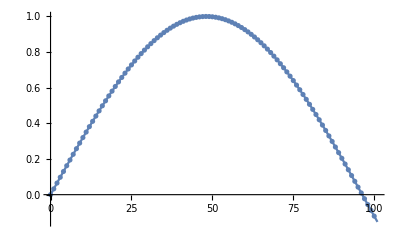

```mathematica
Show[Plot[fn2,{c,0,Length[dat]}],ListPlot[dat]]
```

```mathematica
Total@Table[(fn2-dat[[c+1,2]])^2,{c,0,Length[dat]-1}]
```

0.210056

```mathematica
fn2/.c->1
```

0.320487

```mathematica
dat
```

{{0.,0.},{1.,0.320478},{2.,0.607149}}

```mathematica
makmake
```